# Coursework Part 2

## Exercise 1

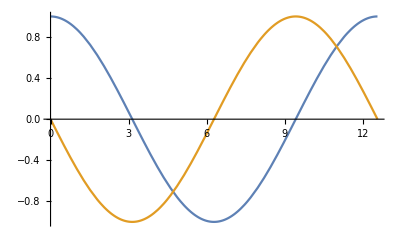

```mathematica
wMatrixRWA=Ω/2 PauliMatrix[2];
stateVec=Table[Subscript[c, i][t],{i,2}];
initStateVec={1,0};
tdseEqnsRWA=Table[{Subscript[c, i]'[t]==I(wMatrixRWA.stateVec)[[i]],Subscript[c, i][0]==initStateVec[[i]]},{i,2}];
tMax=4 Pi;
solRWA=NDSolve[tdseEqnsRWA/.Ω->1,stateVec,{t,0,tMax}];
solFnRWA=stateVec/.First[solRWA];
Plot[solFnRWA,{t,0,tMax}]
```

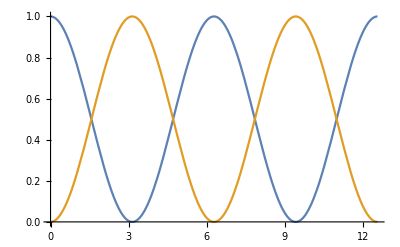

```mathematica
solFnRWAProb=Abs[solFnRWA]^2;
Plot[solFnRWAProb,{t,0,tMax}]
```

i) The plot shows the probabilities for the upper (blue line) and lower (red line) eigenstate as functions of time after setting up the system as in the upper energy state and letting it evolve with time.

ii) same problem with σ_x

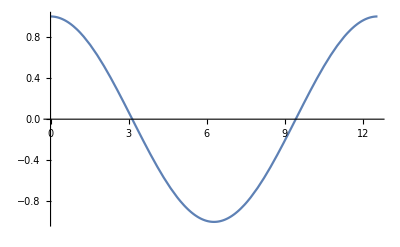

-Graphics-

```mathematica
wMatrixRWA=Ω/2 PauliMatrix[1];
tdseEqnsRWA=Table[{Subscript[c, i]'[t]==I(wMatrixRWA.stateVec)[[i]],Subscript[c, i][0]==initStateVec[[i]]},{i,2}];
solRWA=NDSolve[tdseEqnsRWA/.Ω->1,stateVec,{t,0,tMax}];
solFnRWA=stateVec/.First[solRWA];
Plot[solFnRWA,{t,0,tMax}]
solFnRWAProb=Abs[solFnRWA]^2;
Plot[solFnRWAProb,{t,0,tMax}]
```

## Exercise 2

iii)

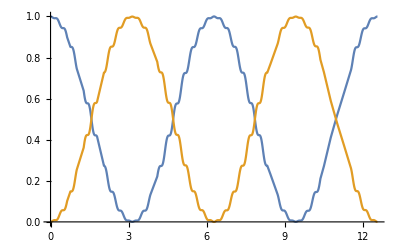

```mathematica
wMatrixLab=-w12/2 PauliMatrix[3]-Ω Cos[ω t] PauliMatrix[2]/.w12->ω+Δ;
tdseEqns=Table[{Subscript[c, i]'[t]==I(wMatrixLab.stateVec)[[i]],Subscript[c, i][0]==initStateVec[[i]]},{i,2}];
tdseSolraw= NDSolve[tdseEqns/.{ω->10Ω, Δ-> 0}/.Ω-> 1, stateVec, {t,0,tMax}];
tdseSol=Abs[stateVec/.First[tdseSolraw]]^2;
Plot[tdseSol,{t,0,tMax}]
```

## Exercise 3

iv)

```mathematica
wMatrixRWA = -Ω/2 PauliMatrix[1]-{{0,0},{0,-Δ}};
T=MatrixExp[-I wMatrixRWA t] ;
T//MatrixForm
RWAstatevec = T.initStateVec;
RWAstatevec//MatrixForm
```

(-(ⅇ^(1/2 ⅈ t (-Δ-√(Δ^2+Ω^2))) (Δ-√(Δ^2+Ω^2)))/(2 √(Δ^2+Ω^2))+(ⅇ^(1/2 ⅈ t (-Δ+√(Δ^2+Ω^2))) (Δ+√(Δ^2+Ω^2)))/(2 √(Δ^2+Ω^2)) | -(ⅇ^(1/2 ⅈ t (-Δ-√(Δ^2+Ω^2))) Ω)/(2 √(Δ^2+Ω^2))+(ⅇ^(1/2 ⅈ t (-Δ+√(Δ^2+Ω^2))) Ω)/(2 √(Δ^2+Ω^2))
-(ⅇ^(1/2 ⅈ t (-Δ-√(Δ^2+Ω^2))) Ω)/(2 √(Δ^2+Ω^2))+(ⅇ^(1/2 ⅈ t (-Δ+√(Δ^2+Ω^2))) Ω)/(2 √(Δ^2+Ω^2)) | -(ⅇ^(1/2 ⅈ t (-Δ-√(Δ^2+Ω^2))) (-Δ-√(Δ^2+Ω^2)))/(2 √(Δ^2+Ω^2))+(ⅇ^(1/2 ⅈ t (-Δ+√(Δ^2+Ω^2))) (-Δ+√(Δ^2+Ω^2)))/(2 √(Δ^2+Ω^2)))

(-(ⅇ^(1/2 ⅈ t (-Δ-√(Δ^2+Ω^2))) (Δ-√(Δ^2+Ω^2)))/(2 √(Δ^2+Ω^2))+(ⅇ^(1/2 ⅈ t (-Δ+√(Δ^2+Ω^2))) (Δ+√(Δ^2+Ω^2)))/(2 √(Δ^2+Ω^2))
-(ⅇ^(1/2 ⅈ t (-Δ-√(Δ^2+Ω^2))) Ω)/(2 √(Δ^2+Ω^2))+(ⅇ^(1/2 ⅈ t (-Δ+√(Δ^2+Ω^2))) Ω)/(2 √(Δ^2+Ω^2)))

v)

```mathematica
Simplify[ExpToTrig[RWAstatevec/.{Δ->0}], assume Ω>0]
```

{Cos[(t Ω)/2],ⅈ Sin[(t Ω)/2]}

vi)

```mathematica
genRabi=Sqrt[Ω^2+Δ^2];
Tlect=Exp[-I Δ t/2] {{Cos[genRabi t/2]-I Δ/genRabi Sin[genRabi t/2], I Ω/genRabi Sin[genRabi t/2]},{I Ω/genRabi Sin[genRabi t/2], Cos[genRabi t/2]+I Δ/genRabi Sin[genRabi t/2]}};
Tlect//MatrixForm
lectSol=Tlect.initStateVec
```

(ⅇ^(-1/2 ⅈ t Δ) (Cos[1/2 t √(Δ^2+Ω^2)]-(ⅈ Δ Sin[1/2 t √(Δ^2+Ω^2)])/(√(Δ^2+Ω^2))) | (ⅈ ⅇ^(-1/2 ⅈ t Δ) Ω Sin[1/2 t √(Δ^2+Ω^2)])/(√(Δ^2+Ω^2))
(ⅈ ⅇ^(-1/2 ⅈ t Δ) Ω Sin[1/2 t √(Δ^2+Ω^2)])/(√(Δ^2+Ω^2)) | ⅇ^(-1/2 ⅈ t Δ) (Cos[1/2 t √(Δ^2+Ω^2)]+(ⅈ Δ Sin[1/2 t √(Δ^2+Ω^2)])/(√(Δ^2+Ω^2))))

{ⅇ^(-1/2 ⅈ t Δ) (Cos[1/2 t √(Δ^2+Ω^2)]-(ⅈ Δ Sin[1/2 t √(Δ^2+Ω^2)])/(√(Δ^2+Ω^2))),(ⅈ ⅇ^(-1/2 ⅈ t Δ) Ω Sin[1/2 t √(Δ^2+Ω^2)])/(√(Δ^2+Ω^2))}

```mathematica
Simplify[lectSol/.Δ->0, assume Ω>0]
```

{Cos[(t Ω)/2],ⅈ Sin[(t Ω)/2]}

vii)

```mathematica
wMatrixRWA2 = Ω/2 PauliMatrix[2]+Δ/2 PauliMatrix[3];
genSol2 = MatrixExp[-I wMatrixRWA2 t];
genSol2//FullForm;
simpleGenSol = FullSimplify[genSol2/.{ Sqrt[-Ω^2-Δ^2]->I Ωeff, 1/Sqrt[-Ω^2-Δ^2]->1/(I Ωeff)}];
simpleGenSol//MatrixForm
```

(Cos[(t Ωeff)/2]-(ⅈ Δ Sin[(t Ωeff)/2])/Ωeff | -(Ω Sin[(t Ωeff)/2])/Ωeff
(Ω Sin[(t Ωeff)/2])/Ωeff | Cos[(t Ωeff)/2]+(ⅈ Δ Sin[(t Ωeff)/2])/Ωeff)

This is the time evolution matrix which is operated on the coefficient vector. One can see that it only differs from the general solution from vi) (lecture 4)  by a phase factor.

viii)

{Abs[Cos[1/2 t √(Δ^2+Ω^2)]-(ⅈ Δ Sin[1/2 t √(Δ^2+Ω^2)])/(√(Δ^2+Ω^2))]^2,Abs[(Ω Sin[1/2 t √(Δ^2+Ω^2)])/(√(Δ^2+Ω^2))]^2}

{Abs[Cos[(5 t)/2]-3/5 ⅈ Sin[(5 t)/2]]^2,16/25 Abs[Sin[(5 t)/2]]^2}

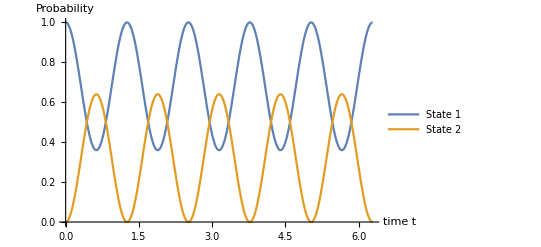

```mathematica
evolvedstate=Abs[simpleGenSol.initStateVec/.Ωeff->genRabi]^2
plotstate=evolvedstate/.{Δ->3,Ω->4}
Plot[plotstate, {t,0,2Pi}, PlotLegends->{"State 1","State 2"}, AxesLabel->{"time t", "Probability"}]
```

ix)
For an arbitrary choice of detuning  Δ and rabi frequency Ω the frequency of the oscillation of the probabilities is always the generalized rabi frequency Ωeff=Sqrt(Ω^2+Δ^2) .  Thus, the frequency of the oscillations for a fixed rabi frequency increases with larger  abolsute value of detuning. At the same time
x)

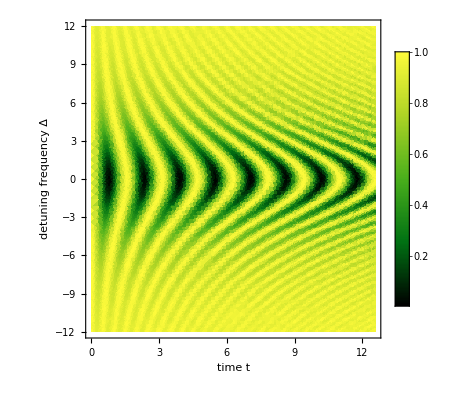

```mathematica
DensityPlot[evolvedstate[[1]]/.{Ω->4},{t, 0, 4 Pi}, {Δ,-12, 12}, PlotPoints->40, FrameLabel->{"time t", "detuning frequency Δ"},ColorFunction->ColorData["AvocadoColors"],PlotLegends->Automatic]
```